# Backwards Facing Step

The SC map should have 
	f'(z)=C √(z/(z-1))
The backwards facing step should have a corner with angle -π/2 at z=0 and a corner with angle π/2 at z=1.

It is a pain to make an analytic integral which respects the appropriate branch cut

```mathematica
Clear[F,z]
F[z_]=Integrate[√(z/(z-1)),z]
FullSimplify[F'[z]]
Clear[F,z]
```

(z (√(-((-1+z) z))+ArcSin[√(1-z)]))/(√(z/(-1+z)) √(-((-1+z) z)))

√(z/(-1+z))

```mathematica
TabView[{
ComplexPlot3D[√(z/(z-1)),{z,2}],
ComplexPlot3D[(√z)/(√(z-1)),{z,2}],
ComplexPlot3D[(z (√(-((-1+z) z))+ArcSin[√(1-z)]))/(√(z/(-1+z)) √(-((-1+z) z))),{z,2}]
}]
```

123

We are going to simply integrate numerically starting (on the positive side) at the middle of the branch cut i.e. z_0=0.5+ϵ ⅈ.   As a first pass we are going to integrate along the straight line ζ(t)=z_0(1-t)+z t  for 0≤t≤1. Our parametric definition of the integral gives simply
	F(z)=∫_0^1 fPrime[ζ(t)].ζ'(t)dt

6.93323×10^-10-1. ⅈ

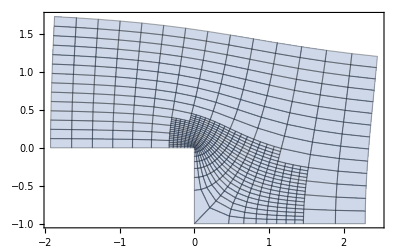

```mathematica
Clear[F,z]
fPrime[z_]:=√(z/(z-1)) 
F[z_]:= 2/π(Module[{ϵ=10^-12,z0},
z0=0.5+ I;
NIntegrate[fPrime[z0*(1-t)+z t]*(z-z0),{t,0,1}]
]-(-0.7218177375894088-0.332635825352444 ⅈ))
F[1]
ParametricPlot[ReIm[F[x+ ⅈ y]],{x,-4,3},{y,0,3},
Mesh->All]
```

```mathematica
π/2.0
```

1.5708

It is working but it would be nice to have the corner in the right place and the step down of size 1.  It would also be nice if it did not look wobbly and did not throw warnings.   The warnings are very specifically to do with the warnings.

What suggestions do people have to fix these issues.

## Analytic Integration Issues

```mathematica
Integrate[√(z/(z-1)),z]
```

(z (√(-((-1+z) z))+ArcSin[√(1-z)]))/(√(z/(-1+z)) √(-((-1+z) z)))

```mathematica
F[z_]:=(z (√(-((-1+z) z))+ArcSin[√(1-z)]))/(√(z/(-1+z)) √(-((-1+z) z)))
ComplexPlot3D[F[z],{z,3}]
```

-Graphics3D-

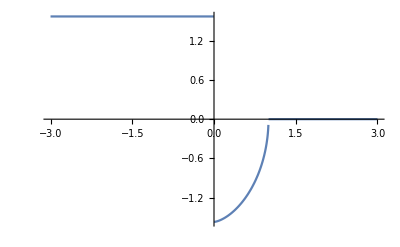

```mathematica
Plot[Im[F[x]],{x,-3,3}]
```

```mathematica
Integrate[√(ζ/(ζ-1)),{ζ,0,z},Re[ζ]>0]
```

Integrate::ilim: Invalid integration variable or limit(s) in Re[ζ]>0.

∫_0^z ∫√(ζ/(-1+ζ))ⅆ(Re[ζ]>0)ⅆζ

```mathematica
ComplexPlot3D[logcut[z],{z,3},
PlotRange->{0,10}]
ComplexPlot3D[Log[z]-logcut[z],{z,3}]
```

-Graphics3D-

-Graphics3D-

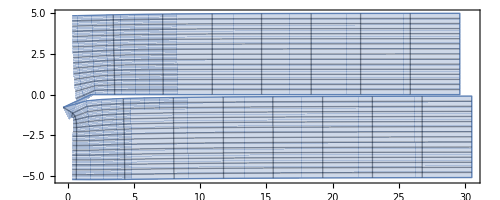

```mathematica
c=1;
(* Define a new log like function *)
logcut[z_]:=Log[z-1]-Log[z]
f[z_]:=c(√(z(z-1))-logcut[√z+√(z-1)])
ParametricPlot[ ReIm[f[x+I y]],{x,-30,30},{y,0,5},
Mesh->Automatic]
```

An analytic function f(z)=ϕ(x,y)+ⅈ ψ(x,y) gives a fluid velocity field
	f'(z)=u(x,y)-ⅈ v(x,y)
satisfying the incompressibility equation
	∂_x u+∂_y v=0
and the irrotational equation
	∂_x v-∂_y u=0.
If you have never seen the 2D curl is is just the third component of the 3D curl of “2D” velocity field 	
	{u(x,y),v(x,y),0}

```mathematica
Curl[{u[x,y],v[x,y],0},{x,y,z}]
```

{0,0,-u^(0,1)[x,y]+v^(1,0)[x,y]}

The point is that the velocity potential ϕ and the stream function ψ  are automatic given any analytic function.  This is like finding a huge library of 2D flows.  Some of those flows were useful in the relatively early development of flight. We do need to be careful about the minis sign on the y-component of the velocity.